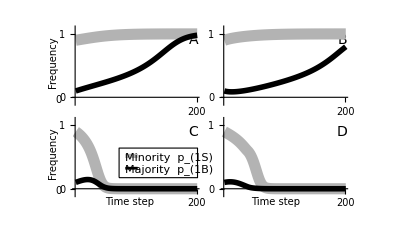

~/Fig7bias.pdf

```mathematica
(*Makes figure 7 with biased norm 2 visitor selection*)

Clear[wik,wnik, Rk, Rik, Vk, Vik, boundsim,a,m,d,g,mu];
Clear[a,bnik, bik,bnink,bink, gk, mnk, mk, dnk, pik, pnik, pink, pnink];

boundsim[
pg1init_,(*(vector) group 1: norm 1, norm 2*)
pg2init_,(*(vector) group 2: norm 1, norm 2*)
tmax_,(*# sims*)
a_,(*prob of assorting on marker*)
m_,(*(vector) proportion of each group that is visitors*)
d_,(*(matrix) relative group sizes: how many times bigger the row group is than the column group*)
g_,(*(vector) inter-ethnic coordination payoff bonus for each group*)
mu_, (*effect of a payoff difference on copying*)
b_ (*bias for norm 2 migrants from group 1*)
]:=Module[{},

(*intialize vectors and matrices*)
p1={pg1init[[1]], pg2init[[1]]}; (*norm 1 in both groups*)
p2={pg1init[[2]], pg2init[[2]]}; (*norm 2 in both groups*)
matg1all={pg1init}; (*matrix holding norm freqs for group 1*)
matg2all={pg2init};
fitg1={1,1}; (*payoff of norms in group 1*)
fitg2={1,1};
fitg1all={fitg1}; (*matrix holding norm payoffs for group 1*)
fitg2all={fitg2};
(*bik=b;
bnik=b;
bink=b;
bnink=b;*)
b21=b;



(*payoff for un-biased norm 1 in group 1*)
Rk=(1-mk)+dnk*mnk;
Vk=mk+dnk*(1-mnk);

rfill11=1-pnik-mk*(1-pnik^bnik);
vfill11=mk*(1-pnik^bnik);

rspace11=1-mk-pnik+pnik*pnik^bnik+pnik*(mk-pnik)*(1-pnik^bnik)/(1-pnik);
vspace11=mk-pnik*pnik^bnik-pnik*(mk-pnik)*(1-pnik^bnik)/(1-pnik);

bRikfill11=rfill11+pink*dnk*mnk;
bVikfill11=vfill11+pink*dnk*(1-mnk);

bRikspace11=rspace11+pink*dnk*mnk;
bVikspace11=vspace11 + pink*dnk*(1-mnk);

bfitnessikFill11=a*((1-mk)*1/bRikfill11*(pink*dnk*mnk*(1+gk)+rfill11*1)+mk*1/bVikfill11*(pink*dnk*(1-mnk)*(1+gk)+vfill11*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rfill11*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vfill11*1)); (*payoff for grp k when biased norm i indivs outnumber spaces in visitor boat*)

bfitnessikSpace11=a*((1-mk)*1/bRikspace11*(pink*dnk*mnk*(1+gk)+rspace11*1)+mk*1/bVikspace11*(pink*dnk*(1-mnk)*(1+gk)+vspace11*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rspace11*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vspace11*1));(*payoff for grp k when spaces in visitor boat outnumber biased norm i indivs*)



(*payoff for biased norm 2 in group 1*)
rfill21=pik-mk*pik^bik;
vfill21=mk*pik^bik;

rspace21=pik*(1-pik^bik-(mk-pik)*(1-pik^bik)/(1-pik));
vspace21=pik*(pik^bik+(mk-pik)*(1-pik^bik)/(1-pik));

bRikfill21=rfill21+pink*dnk*mnk;
bVikfill21=vfill21+pink*dnk*(1-mnk);

bRikspace21=rspace21+pink*dnk*mnk;
bVikspace21=vspace21+pink*dnk*(1-mnk);

bfitnessikFill21=a*((1-mk)*1/bRikfill21*(pink*dnk*mnk*(1+gk)+rfill21*1)+mk*1/bVikfill21*(pink*dnk*(1-mnk)*(1+gk)+vfill21*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rfill21*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vfill21*1)); (*payoff for grp k when biased norm i indivs outnumber spaces in visitor boat*)

bfitnessikFill21zero=
a*(0+
mk*1/bVikfill21*(pink*dnk*(1-mnk)*(1+gk)+vfill21*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rfill21*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vfill21*1)); (*pik=mk and no visitors from the other group: bRikfill21=0*)

bfitnessikSpace21=a*((1-mk)*1/bRikspace21*(pink*dnk*mnk*(1+gk)+rspace21*1)+mk*1/bVikspace21*(pink*dnk*(1-mnk)*(1+gk)+vspace21*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rspace21*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vspace21*1));(*payoff for grp k when spaces in visitor boat outnumber biased norm i indivs*)

bfitnessikSpace21zero=
a*(0+
mk*1/bVikspace21*(pink*dnk*(1-mnk)*(1+gk)+vspace21*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+rspace21*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+vspace21*1));(*No norm i indivs left as residents and no migrants from the other group: bRikspace21=0*)




(*payoff for un-biased norm 1 in group 2*)
rfill12=1-pnink-mnk*(1-pnink^bnink);
vfill12=mnk*(1-pnink^bnink);

rspace12=1-mnk-pnink+pnink*pnink^bnink+pnink*(mnk-pnink)*(1-pnink^bnink)/(1-pnink);
vspace12=mnk-pnink*pnink^bnink-pnink*(mnk-pnink)*(1-pnink^bnink)/(1-pnink);

bRikfill12=pik*(1-mk)+dnk*vfill12;(*visitors from the other group*)
bVikfill12=pik*mk+dnk*rfill12;(*residents from the other group*)

bRikspace12=pik*(1-mk)+dnk*vspace12;
bVikspace12=pik*mk+dnk*rspace12;

bfitnessikFill12=a*((1-mk)*1/bRikfill12*(dnk*vfill12*(1+gk)+pik*(1-mk)*1)+mk*1/bVikfill12*(dnk*rfill12*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(dnk*vfill12*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rfill12*(1+gk)+pik*mk*1)); (*payoff for grp k when biased norm i indivs outnumber spaces in visitor boat*)

bfitnessikSpace12=a*((1-mk)*1/bRikspace12*(dnk*vspace12*(1+gk)+pik*(1-mk)*1)+mk*1/bVikspace12*(dnk*rspace12*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(dnk*vspace12*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rspace12*(1+gk)+pik*mk*1)); (*payoff for grp k when spaces in visitor boat outnumber biased norm i indivs*)



(*payoff for un-biased norm 2 in group 2*)
rfill22=pink-mnk*pink^bink;
vfill22=mnk*pink^bink;

rspace22=pink*(1-pink^bink-(mnk-pink)*(1-pink^bink)/(1-pink));
vspace22=pink*(pink^bink+(mnk-pink)*(1-pink^bink)/(1-pink));

bRikfill22=pik*(1-mk)+dnk*vfill22;(*visitors from the other group*)
bVikfill22=pik*mk+dnk*rfill22;(*residents from the other group*)

bRikspace22=pik*(1-mk)+dnk*vspace22;
bVikspace22=pik*mk+dnk*rspace22;

bfitnessikFill22=a*((1-mk)*1/bRikfill22*(dnk*vfill22*(1+gk)+pik*(1-mk)*1)+mk*1/bVikfill22*(dnk*rfill22*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(dnk*vfill22*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rfill22*(1+gk)+pik*mk*1)); (*payoff for grp k when biased norm i indivs outnumber spaces in visitor boat*)

bfitnessikFill22zero=a*((1-mk)*1/bRikfill22*(dnk*vfill22*(1+gk)+pik*(1-mk)*1)+
0)+(1-a)*((1-mk)*1/Rk*(dnk*vfill22*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rfill22*(1+gk)+pik*mk*1)); (*pink=mnk and no visitors from this group: bVikfill22=0*)

bfitnessikSpace22=a*((1-mk)*1/bRikspace22*(dnk*vspace22*(1+gk)+pik*(1-mk)*1)+mk*1/bVikspace22*(dnk*rspace22*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(dnk*vspace22*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rspace22*(1+gk)+pik*mk*1)); (*payoff for grp k when spaces in visitor boat outnumber biased norm i indivs*)

bfitnessikSpace22zero=a*((1-mk)*1/bRikspace22*(dnk*vspace22*(1+gk)+pik*(1-mk)*1)+
0)+(1-a)*((1-mk)*1/Rk*(dnk*vspace22*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(dnk*rspace22*(1+gk)+pik*mk*1)); (*no norm i residents in the other group and no visitors from this group: bVikspace22=0*)



(*new phenotype freqs after copying*)
pikprime=pik+pik*pnik*mu*(wik-wnik);


(*simulation*)
For    [t=1,t<=tmax,t++,

(*update norm frequencies for the two groups*)
p1k=p1; (*norm 1 freqs*)
p2k=p2; (*norm 2 freqs*)

If[p2[[2]]<p2[[1]],b21=1,b21=b]; (*if freq norm 2 in group 2 is less than freq norm 2 in group 1, then group 1 indivs with norm 2 will not be biased to visit group 2*)

For[k=1,k≤2,k++,(*loop over groups*)

If[k==1,nk=2,nk=1]; (*adjust index of other group*)



(*phenotype payoffs*)

(*w1k*)
If[p1k=={0,0},
w1k=0,
If[k==1,
If[p2k[[k]]>=m[[k]],
{ (*visitor boat can be filled with biased indivs*)
w1k=bfitnessikFill11/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p1k[[nk]],pik->p1k[[k]],pnik->p2k[[k]],
bnik->b21
}
},
{(*visitor boat cannot be filled with biased indivs*)
w1k=bfitnessikSpace11/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p1k[[nk]],pik->p1k[[k]],pnik->p2k[[k]],
bnik->b21
}
}
],(*if visitor boat can be filled*)
If[p2k[[nk]]>=m[[nk]],
{ (*visitor boat can be filled with biased indivs*)
w1k=bfitnessikFill12/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p1k[[nk]],pik->p1k[[k]],pnink->p2k[[nk]],
bnink->b21
}
},
{(*visitor boat cannot be filled with biased indivs*)
w1k=bfitnessikSpace12/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p1k[[nk]],pik->p1k[[k]],pnink->p2k[[nk]],
bnink->b21
}
}
](*if visitor boat can be filled*)
](*if k==1*)
];(*if p1k == 0,0*)


(*w2k*)
If[p2k=={0,0},
w2k=0,
If[k==1,
If[p2k[[k]]>=m[[k]],
{ (*visitor boat can be filled with biased indivs*)
test1=bRikfill21/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
};
(*Print["test1=0: ", test1==0];*)
If[test1==0,
w2k=bfitnessikFill21zero/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
},
w2k=bfitnessikFill21/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
}
](*if bRikfill21=0*)
},
{(*visitor boat cannot be filled with biased indivs*)
test2=bRikspace21/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
};
(*Print["test2=0: ", test2==0];*)
If[test2==0,
w2k=bfitnessikSpace21zero/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
},
w2k=bfitnessikSpace21/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bik->b21
}
](*if bRikspace21=0*)
}
], (*if visitor boat can be filled*)
If[p2k[[nk]]>=m[[nk]],
{ (*visitor boat can be filled with biased indivs*)
test3=bVikfill22/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
};
(*Print["test3=0: ", test3==0];*)
If[test3==0,
w2k=bfitnessikFill22zero/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
},
w2k=bfitnessikFill22/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
}
](*if bRikfill22=0*)
},
{(*visitor boat cannot be filled with biased indivs*)
test4=bVikspace22/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
};
(*Print["test4=0: ", test4==0];*)
If[test4==0,
w2k=bfitnessikSpace22zero/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
},
w2k=bfitnessikSpace22/.{
dnk->d[[nk,k]],gk->g[[k]],
mnk->m[[nk]],mk->m[[k]],
pink->p2k[[nk]],pik->p2k[[k]],
bink->b21
}
](*if bVikspace22=0*)
}
] (*if visitor boat can be filled*)
](*if k==1*)
];(*if p1k == 0,0*)



(*Recursion*)
p1kprime=pikprime /.
{pik->p1k[[k]],
pnik->p2k[[k]],
wik->w1k,
wnik->w2k};

p2kprime=1-p1kprime;


(*update phenotype and payoff matrices*)
If [k==1,
{
p1={p1kprime,p1[[2]]}, (*just update freq of norm 1 for group 1*)
p2={p2kprime,p2[[2]]},(*just norm 2 for group 1*)
fitg1={w1k,w2k}
},
{
p1 = {p1[[1]], p1kprime},
(*just update freq of norm 1 for group 2*)
p2 = {p2[[1]], p2kprime},(*just norm 2 for group 2*)
fitg2={w1k,w2k}
}
](*if/else*)

];(*for k*)


(*accumulate phenotype freqs and payoffs across sims*)
matg1all=Join[matg1all,{{p1[[1]],p2[[1]]}}];
matg2all=Join[matg2all,{{p1[[2]],p2[[2]]}}];
fitg1all=Join[fitg1all, {fitg1}];
fitg2all=Join[fitg2all, {fitg2}];

](*for t*)

];(*boundsim*)



(*A*************************majority controls resources*******************************)

boundsim[
pg1init={0.9,0.1},  (*group 1: norm 1, norm 2*)
pg2init={0.1,0.9}, (*group 2: norm 1, norm 2*)

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
b=1(*bias for norm 2 migrants from group 1, 0 is complete bias, 1 is no bias*)
];


(*
Print["Ending freq of norm 0 in both groups: ", p1,"

Matrices of norm freqs in each group: 
",
matg1all //MatrixForm,
matg2all //MatrixForm, "

Matrices of payoffs of norms in each group:
",
fitg1all//MatrixForm,
fitg2all//MatrixForm
] 
*)

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3a=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,Black},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0"},{1,"1"}}}
];
(*
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


(*B****************majority controls resources, bias*************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 1, norm 2*)
pg2init={0.1,0.9}, (*group 2: norm 1, norm 2*)

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
b=0.1(*bias for norm 2 migrants from group 1, 0 is complete bias, 1 is no bias*)
];


(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)


(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3b=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,White},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0",{0,0}},{1,"1",{0,0}}}}
];




(*C************************majority resources, high migration*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 1, norm 2*)
pg2init={0.1,0.9}, (*group 2: norm 1, norm 2*)

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.4,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
b=1(*bias for norm 2 migrants from group 1, 0 is complete bias, 1 is no bias*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3c=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,Black},
Ticks->{{{100,""},{200,"200"}},{{0,"0"},{1,"1"}}}
];


(*D************************minority homeland, lots of visitors*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.4,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
b=0.1(*bias for norm 2 migrants from group 1, 0 is complete bias, 1 is no bias*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3d=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,White},
Ticks->{{{100,""},{200,"200"}},{{0,"0",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(****************************************assemble plots into Fig 7 (formerly fig 5)*)
Fig5bias=Panel[
GraphicsGrid[
{{f3a,f3b},{f3c,f3d}},

Spacings->{
{
Scaled[0.4],
Scaled[0],
Scaled[0.2]
},
{
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["A",14],{380,-45}],
Inset[Style["B",14],{740,-45}],
Inset[Style["C",14],{380,-270}],
Inset[Style["D",14],{740,-270}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-100}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-320}],
Inset[Style["Time step",10],{225,-440}],
Inset[Style["Time step",10],{580,-440}],
Inset[Style["0",10],{54,-190}],
Inset[Style["0",10],{54,-412}],

x=40;
y=-230;
{EdgeForm[Thin],White,Rectangle[{160+x,-78+y},{350+x,-150+y}]},
Inset[Style["Minority ",10]Style[Subscript[Style["p",Italic,10],Style["1S",8]],Italic,10],{280+x,-100+y}],
Inset[Style["Majority ",10]Style[Subscript[Style["p",Italic,10],Style["1B",8]],Italic,10],{280+x,-130+y}],
{AbsoluteThickness[3],GrayLevel[0.7],Line[{{175+x,-97+y},{205+x,-97+y}}]},
{AbsoluteThickness[2],Black,Line[{{175+x,-127+y},{205+x,-127+y}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["~/Fig7bias.pdf",Fig5bias,"PDF"]
(*Export["~/Fig7bias.pdf",Fig5bias,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
*)
```